```mathematica
(*Compute the repo root from the notebook location*)
repoRoot=ParentDirectory@NotebookDirectory[];
repoAppDir=FileNameJoin[{repoRoot,"mma"}];

If[!MemberQ[$Path,repoAppDir],AppendTo[$Path,repoAppDir];];

ClearAll["LocalF1`*"];
<<LocalF1`;
```

```mathematica
{r,df,db,ch2}.Sigma.{1,m,t,td}
```

-ch2+(-db+df) m+(db+2 df) t-r td

```mathematica
Factor[64-80 u+153 u^2]
```

64-80 u+153 u^2

```mathematica
um=8/153 (5-8 ⅈ √2);
```

```mathematica
Simplify@Abs[8/153 (5-8 ⅈ √2)]
```

8/(3 √17)

```mathematica
points=Table[8/153 (5-8 ⅈ √2)+1/10Exp[I x Degree], {x, 60, 150, 10}];
```

{{u→-8/9},{u→-8/9},{u→8/153 (5-8 ⅈ √2)},{u→8/153 (5+8 ⅈ √2)}}

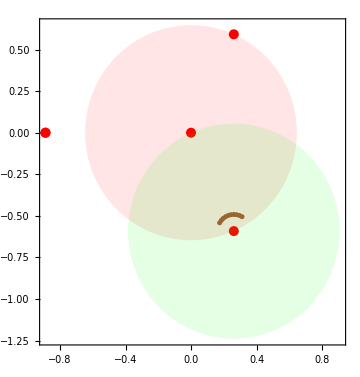

```mathematica
Solve[MirrorCurveDelta2[-27/256,u]==0, u]
Graphics[{PointSize[.02],Red,Point[ReIm/@Join[u/.%,{0}]], Opacity[.1,Red],Disk[ReIm[0],8/(3 √17)], Opacity[.1,Green], Disk[ReIm[8/153 (5-8 ⅈ √2)],8/(3 √17)], PointSize[.01],Opacity[1,Brown], Point[ReIm/@points]},Frame->True,Axes->True,ImageSize->Medium]
```

```mathematica
FullSimplify[Series[MirrorCurveJ2[-27/256,u], {u,8/153 (5-8 ⅈ √2),2}]]
```

(2048 ⅈ (6976 ⅈ+11369 √2))/(5688387 (u-8/153 (5-8 ⅈ √2)))+(16 (15427825+3424 ⅈ √2))/334611+((-434574656-708231089 ⅈ √2) (u-8/153 (5-8 ⅈ √2)))/34992+((-5229553881691+3968930012384 ⅈ √2) (u-8/153 (5-8 ⅈ √2))^2)/13436928+O[u-8/153 (5-8 ⅈ √2)]^3

```mathematica
pf1=FullSimplify[Collect[FullSimplify[PicardFuchs2[f[u],-27/256,u]], {f[u],f'[u],f''[u]}]/.{f->Function[u, F[u-8/153 (5-8 ⅈ √2)]]}/.{u->z+8/153 (5-8 ⅈ √2)}]
```

(306 (-2048 (235939 ⅈ+103816 √2)+153 z (256 (-76977 ⅈ+27824 √2)+153 z (32 (-1333 ⅈ+6000 √2)+153 (1000 ⅈ+768 √2+459 ⅈ z) z))) F'[z])/((40 ⅈ+64 √2+153 ⅈ z)^2 (176 ⅈ+64 √2+153 ⅈ z)^2 (128 √2+153 ⅈ z) z)-(18 (-8192 (24 ⅈ+√2)+17 z (128 (-393 ⅈ+500 √2)+153 (500 ⅈ+576 √2+459 ⅈ z) z)) F''[z])/((40 ⅈ+64 √2+153 ⅈ z) (176 ⅈ+64 √2+153 ⅈ z) (128 √2+153 ⅈ z) z)+F^(3)[z]

```mathematica
currentOrder=1;
A0=z;
coeffList={};
MaxTerms=30;
```

```mathematica
Monitor[Do[
var=Symbol["a"<>ToString[currentOrder+1]];
A0=A0+var z^(currentOrder+1);
limit=Limit[z^(2-currentOrder)(pf1/.F->Function[z,Evaluate[A0]]), z->0];
sol=FullSimplify[Solve[limit==0,var]];
A0=A0/.First[sol];
AppendTo[coeffList, var/.First[sol]];
currentOrder=currentOrder+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
N[Abs[(Last[coeffList])^(-1/currentOrder)],50]
```

0.70143210077490743622878747975553682307352915158096

```mathematica
N[Abs[8/153 (5-8 ⅈ √2)]]
```

0.646762

```mathematica
curr=1;
A1=0;
coeffList2={};
MaxTerms=15;
```

```mathematica
powers=z^Range[2,MaxTerms];
```

```mathematica
Monitor[Do[
var=Symbol["b"<>ToString[curr+1]];
limit=Limit[z^(2-curr)(pf1/.F->Function[z,Evaluate[Log[z](z+coeffList[[;;curr]].powers[[;;curr]])+A1+var z^(curr+1)]]),z->0];
sol=Solve[limit==0,var];
A1=A1+FullSimplify[var z^(curr+1)/.First[sol]];
AppendTo[coeffList2, FullSimplify[var/.First[sol]]];
curr=curr+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

Limit::ztest: Unable to decide whether numeric quantities {-307/288-(14797 ⅈ)/(4608 √2)-1985481/(64 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)-(36098667 ⅈ)/(512 √2 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2),307/288+(14797 ⅈ)/(4608 √2)+1985481/(64 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)+(36098667 ⅈ)/(512 √2 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)} are equal to zero. Assuming they are.

Part::take: Cannot take positions 1 through 15 in {z^2,z^3,z^4,z^5,z^6,z^7,z^8,z^9,z^10,z^11,z^12,z^13,z^14,z^15}.

$Aborted

```mathematica
Phi1=z+coeffList[[;;MaxTerms]].powers[[;;MaxTerms]];
Phi2=Log[z]Phi1+A1;
```

```mathematica
Series[pf1/.F->Function[z,Evaluate[Phi1]], {z,0,MaxTerms-2}]
```

O[z]^14

```mathematica
Series[pf1/.F->Function[z,Evaluate[Phi2]], {z,0,MaxTerms-2}]
```

O[z]^14

```mathematica
Solve[KerrDoranElFromb[b]==-27/256,b]
Simplify[KerrDoranUrFromb[b]/.%]
```

{{b→1},{b→1},{b→1},{b→1},{b→},{b→},{b→},{b→}}

{-8/9,-8/9,-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2),8/153 (5+8 ⅈ √2),8/153 (5-8 ⅈ √2)}

```mathematica
b0=;
```

```mathematica
points
```

{8/153 (5-8 ⅈ √2)+1/10 ⅇ^(60 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(70 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(80 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(90 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(100 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(110 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(120 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(130 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(140 ⅈ °),8/153 (5-8 ⅈ √2)+1/10 ⅇ^(150 ⅈ °)}

```mathematica
N[fT[-27/256,points[[1]],450,6],50]
```

0.01395739453772066108081509743149555767627193010897+0.19139413413021919109265763118782299168359825164888 ⅈ

```mathematica
N[fTD[-27/256,points[[1]],450,6],50]
```

-0.02385785484379432687255268645692223348580159118817+0.038944200517745179575824000548592799049282153471391 ⅈ

```mathematica
N[Log[-27/256]/3/(2Pi I)]
```

0.166667+0.119331 ⅈ

```mathematica
ttable=Table[N[fT[-27/256,p,450,6],50], {p, points}];
tdtable=Table[N[fTD[-27/256,p,450,6],50], {p, points}];
```

```mathematica
N[a+b Log[-27/256]/3/(2Pi I)+c Phi1+d Phi2/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-ttable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,c,d}]]
```

{a→(-0.01363180547108507615805059758677360659402588282+0.16569532254606235627125864609221678837125933634 ⅈ)-(0.16666666666666666666666666666666666666666666667+0.1193312239205055688632062684312975421304002217 ⅈ) b,c→(0.229419128979544148222207403853877692094605791+0.0517397481746165682867473147707298299850326039 ⅈ)+(0.+0. ⅈ) b,d→(-0.0628807128328707319308959215124094398615047099+0.025605488140369114041658174016110096281950091 ⅈ)+(0.+0. ⅈ) b}

```mathematica
Chop[c/.sol]
```

0.229419128979544148222207403853877692094605791+0.0517397481746165682867473147707298299850326039 ⅈ

```mathematica
Chop[d/.sol]
```

-0.0628807128328707319308959215124094398615047099+0.025605488140369114041658174016110096281950091 ⅈ

```mathematica
FullSimplify[(b^2+b+1)(b^2+4b+1)^2/(1-b)/(b+1)^5/.{b->b0}]
N[%/4/Pi^2]
```

-1/16 √(1316-(1817 ⅈ)/(√2))

-0.0628807+0.0256055 ⅈ

```mathematica
B0=-1/16 √(1316-(1817 ⅈ)/(√2));
N[%]
```

-2.48243+1.01086 ⅈ

```mathematica
m0=Log[-27/256]/3/(2Pi I);
```

```mathematica
Q0=-2Pi(2Pi KerrDoranQ[b0]+Pi/6);
```

```mathematica
B1=FullSimplify[Log[(b^3 (b^2+b+1) (b^2+4 b+1)^2)/(1-b^2)^6]/.{b->b0}];
```

```mathematica
{B0 Phi1, B0 Phi2+B0 B1 Phi1+Q0}
```

```mathematica
N[a+b(B0 Phi1/(4Pi^2))+c(B0 Phi2+B0 B1 Phi1+Q0)/(4Pi^2)/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-ttable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,b,c}]]
```

{a→0.249999885897328814320942060847849627565101228882+0.1193311453119717302591546930258152812135520996233 ⅈ,b→-1.000002153740584376540706327649381642397171990338-3.14159280564084448825045518095565441919893128848 ⅈ,c→0.9999996398961416810812092983131168127714110189862-3.750239392137625020441543554145765272637618935272×10^-7 ⅈ}

```mathematica
N[a+b(B0 Phi1/(4Pi^2))+c(B0 Phi2+B0 B1 Phi1+Q0)/(4Pi^2)/.z->points-8/153 (5-8 ⅈ √2),50];
lhs=%-tdtable;
```

```mathematica
sol=First[Solve[Thread[lhs[[{1,3,6}]]==0],{a,b,c}]]
```

{a→-1.932569893460855193341624493557253803362112809985×10^-8-2.905685093505576973717461031342638845734023459811×10^-8 ⅈ,b→-4.893823395827432062385842924450780587062592013359×10^-7-6.283185544244929518392134466377295012256965752201 ⅈ,c→-4.911440388058343580942113500052902764542002562237×10^-8-1.213842839481134810232788996304191417297846725665×10^-7 ⅈ}

```mathematica
2Pi I/(4Pi^2)
```

ⅈ/(2 π)

```mathematica
data=Table[N[{{1,0,0,0},{0,1,0,0},{1/12,1,(-1-Pi I)/(4Pi^2),1/(4Pi^2)}, {0, 0, -I/(2Pi),0}}.{1,m0,B0 Phi1, B0 Phi2+B0 B1 Phi1+Q0}/.z->p-8/153 (5-8 ⅈ √2),50], {p,points}];
```

```mathematica
N[1/12+m0]
```

0.25+0.119331 ⅈ

```mathematica
Chop[data[[All,4]]-tdtable]
```

{1.6948647337153919178655468694391643400731×10^-10 ⅈ,0,0,0,0,0,0,0,0,0}

```mathematica
N[Log[-27/256]/3/(2Pi I)]
```

0.166667+0.119331 ⅈ

```mathematica
N[1/4/Pi^2]
```

0.0253303

```mathematica
FullSimplify[KerrDoranElFromb[b]/.Solve[b+1/b==t,b]]
```

{-(1+t)^3/(2+t)^4,-(1+t)^3/(2+t)^4}

```mathematica
Expand[Solve[-(1+t)^3/(2+t)^4==-27/256,t]]
FullSimplify[FullSimplify[KerrDoranUrFromb[b]/.First@Solve[b+1/b==t,b]]/.%]
```

{{t→2},{t→2},{t→-34/27-(4 ⅈ √2)/27},{t→-34/27+(4 ⅈ √2)/27}}

{-8/9,-8/9,8/153 (5-8 ⅈ √2),8/153 (5+8 ⅈ √2)}

```mathematica
Simplify[Solve[b+1/b==-34/27-(4 ⅈ √2)/27,b]]
N[%]
```

{{b→1/27 (-17-2 ⅈ √2-2 √(-112+17 ⅈ √2))},{b→1/27 (-17-2 ⅈ √2+2 √(-112+17 ⅈ √2))}}

{{b→-0.713292-0.893135 ⅈ},{b→-0.545967+0.683621 ⅈ}}

```mathematica
Simplify[Solve[b+1/b==-34/27+(4 ⅈ √2)/27,b]]
N[%]
```

{{b→1/27 (-17+2 ⅈ √2-2 √(-112-17 ⅈ √2))},{b→1/27 (-17+2 ⅈ √2+2 √(-112-17 ⅈ √2))}}

{{b→-0.713292+0.893135 ⅈ},{b→-0.545967-0.683621 ⅈ}}

```mathematica
A1
```

(37 (-160-239 ⅈ √2) z^2)/12288+((-2043093721+1720477504 ⅈ √2) z^3)/1528823808+((2086639425395552+418368966120049 ⅈ √2) z^4)/676302730297344+((-103471612788051235141-514600243491389263232 ⅈ √2) z^5)/155820149060508057600+((-1251684398894414490581744+550747535043894401229143 ⅈ √2) z^6)/215405774061246338826240+((6365447274290270956700933197763+3075374505916219157729159261056 ⅈ √2) z^7)/778190408589390933380070113280+((86442510337852572452005432795943392-327411395470306499903897952441574459 ⅈ √2) z^8)/32785384253987779849283319606804480+((-199205464767090986851493321833932546812549+33062886686648087984468716341867008119040 ⅈ √2) z^9)/9789663281625944682548240381280446840832+((745693674664946900994593163011689369725028932128+699499070501821116359337270813546495062292789031 ⅈ √2) z^10)/40599691561559117787464062509246269138298470400+((197302035759641704985708840818824928185954948875452159-249836223317697023395793129922355301202474159913084288 ⅈ √2) z^11)/9054835529838157674608304962062169516361120617594880+((-2975726307921955032351546921659216060234194820956696030112-197471590175069345693589289577537519746136817709582785547 ⅈ √2) z^12)/45517835041630069706830984652926338688791320515502407680+((26063412258167655167382075876548142321629272358503696110357475367+55202525107892983741756878592184228361314102893792663201409766016 ⅈ √2) z^13)/850730521784148001064017031050456610557766842418124743654768640+((892635598879658575457304592716425190385985654134434474431513605696288-574099990107134097547131313094993815303993689583472648501638743219745 ⅈ √2) z^14)/8443434987898300899175671801096470286200408390473548225024066846720+((-32261316823004339954109240906498074396246288372225298767631321349941974099-10100969851677208763308142773750130725639759909526513797746915692359350016 ⅈ √2) z^15)/166745778961008730900292124254796578909192065128437615232475285841510400+((-17106357958358367384747065306267766984544583116684635368537475197090758777312+13100472234537729803458477794748840439864905648374515832681797714222563335394219 ⅈ √2) z^16)/59010397397938808216720341137876682415121180373389352780127701797709818101760

```mathematica
Expand[-2Pi(2Pi Q+Pi/6)]
Simplify[1/12+m+%/(4Pi^2)]
```

-π^2/3-4 π^2 Q

m-Q

```mathematica
B0
```

-1/16 √(1316-(1817 ⅈ)/(√2))

```mathematica
B1
```

Log[(6976+11369 ⅈ √2)/110592]

```mathematica
-4Pi^2Q-Po
```

### At u = up

```mathematica
l0=-27/256;
up=8/153 (5+8 ⅈ √2);
```

```mathematica
points=Table[1/10Exp[I x Degree], {x, 180, 300, 10}];
```

{{u→-8/9},{u→-8/9},{u→8/153 (5-8 ⅈ √2)},{u→8/153 (5+8 ⅈ √2)}}

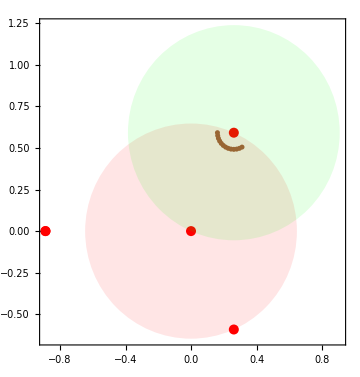

```mathematica
Solve[MirrorCurveDelta2[-27/256,u]==0, u]
Graphics[{PointSize[.02],Red,Point[ReIm/@Join[u/.%,{0}]], Opacity[.1,Red],Disk[ReIm[0],8/(3 √17)], Opacity[.1,Green], Disk[ReIm[up],8/(3 √17)], PointSize[.01],Opacity[1,Brown], Point[ReIm/@(up+points)]},Frame->True,Axes->True,ImageSize->Medium]
```

```mathematica
{b1,b2}=b/.Solve[Thread[KerrDoranElUrFromb[b]=={l0,up}],b]
```

{,}

```mathematica
pf1=Simplify[PicardFuchs2[ff[u],l0,u]/.ff->Function[u,F[u-up]]/.u->z+up];
```

```mathematica
a1=FullSimplify@Together@Coefficient[pf1,Derivative[1][F][z]];
a2=FullSimplify@Together@Coefficient[pf1,Derivative[2][F][z]];
a3=FullSimplify@Together@Coefficient[pf1,Derivative[3][F][z]];
pfop[f_]:=a1 D[f,z]+a2 D[f,{z,2}]+a3 D[f,{z,3}];
```

```mathematica
pfop[f[z]]
```

(306 (2048 (235939 ⅈ-103816 √2)+153 z (256 (76977 ⅈ+27824 √2)+153 z (32 (1333 ⅈ+6000 √2)+153 (-1000 ⅈ+768 √2-459 ⅈ z) z))) f'[z])/((128 √2-153 ⅈ z) (40 ⅈ-64 √2+153 ⅈ z)^2 (176 ⅈ-64 √2+153 ⅈ z)^2 z)+(162 (-1048576 (48 ⅈ+287 √2)+17 z (-16384 (-14071 ⅈ+6860 √2)+17 z (512 (88907 ⅈ+26484 √2)+153 z (32 (2913 ⅈ+9184 √2)+153 (-1148 ⅈ+960 √2-459 ⅈ z) z)))) f''[z])/((128 √2-153 ⅈ z) (40 ⅈ-64 √2+153 ⅈ z)^2 (176 ⅈ-64 √2+153 ⅈ z)^2 z)+f^(3)[z]

```mathematica
currentOrder=1;
A0=z;
coeffList={};
MaxTerms=100;
```

```mathematica
Monitor[Do[
var=Symbol["cof"<>ToString[currentOrder+1]];
A0=A0+var z^(currentOrder+1);
limit=Limit[z^(2-currentOrder)pfop[A0], z->0];
sol=FullSimplify[Solve[limit==0,var]];
A0=A0/.First[sol];
AppendTo[coeffList, var/.First[sol]];
currentOrder=currentOrder+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

```mathematica
curr=1;
A1=0;
coeffList2={};
MaxTerms=15;
```

```mathematica
powers=z^Range[2,MaxTerms+5];
```

```mathematica
Monitor[Do[
var=Symbol["cofff"<>ToString[curr+1]];
limit=Limit[z^(2-curr)pfop[Log[z](z+coeffList[[;;curr]].powers[[;;curr]])+A1+var z^(curr+1)],z->0];
sol=Solve[limit==0,var];
A1=A1+FullSimplify[var z^(curr+1)/.First[sol]];
AppendTo[coeffList2, FullSimplify[var/.First[sol]]];
curr=curr+1;
, {i, MaxTerms}], ProgressIndicator[i/MaxTerms]]
```

Limit::ztest: Unable to decide whether numeric quantities {-307/288-(14797 ⅈ)/(4608 √2)-1985481/(64 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)-(36098667 ⅈ)/(512 √2 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2),307/288+(14797 ⅈ)/(4608 √2)+1985481/(64 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)+(36098667 ⅈ)/(512 √2 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)} are equal to zero. Assuming they are.

$Aborted

```mathematica
co1=FullSimplify[(b^2+b+1)(b^2+4b+1)^2/(1-b)/(b+1)^5/.b->b2]
co2=FullSimplify[Log[(b^3 (b^2+b+1) (b^2+4 b+1)^2)/(1-b^2)^6]/.{b->b2}]
```

1/16 √(1316+(1817 ⅈ)/(√2))

Log[(6976-11369 ⅈ √2)/110592]

```mathematica
Q0=KerrDoranQ[b2];
```

```mathematica
phi1=co1(z+coeffList[[;;15]].powers[[;;15]]);
phi2=co1(Log[z]phi1+A1)+co1 co2 phi1-4Pi^2 Q0;
```

```mathematica
phi1=z+coeffList[[;;15]].powers[[;;15]];
phi2=Log[z]phi1+A1;
```

```mathematica
Simplify[Series[{pfop[phi1], pfop[phi2]},{z,0,13}]]
```

{O[z]^14,O[z]^14}

```mathematica
ClearAll[a,b,c,d,e,f];
n0=Table[N[{{a,b,c},{d,e,f}}.{1,phi1,phi2}/.{z->p},50], {p,points}];
```

```mathematica
n1=Table[N[{fT[l0,up+p,350,3],fTD[l0,up+p,350,3]},50], {p,points}];
```

```mathematica
Dimensions[n0-n1]
```

{13,2}

```mathematica
sol=First@Solve[Thread[RandomSample[Flatten[n0-n1],6]==0], {a,b,c,d,e,f}]
```

{a→0.3469651370235028831176631083894356215556802435393+0.1656953189836077524721955079731946882275730943282 ⅈ,b→-0.2294190657311805255216449072771085289243225696818+0.05173978273488391767674905306624924547724410658516 ⅈ,c→0.06288074506990312460197818258152689996902646035733+0.02560547376922555869931876992767036571532930975513 ⅈ,d→0.5408954110727213019474865168784530823260011624266+0.4970859569467336199604543243305812370537248539783 ⅈ,e→-0.5273732605853090324718423571665335831300873279511-0.2398720252913251467190256003275229225219514426881 ⅈ,f→0.1886422352373278390112903651659633387790784050273+0.07681642133814384119829531280657458439316992788106 ⅈ}

```mathematica
MatrixForm[N[{{a,b,c},{d,e,f}}/.sol]]
```

(0.346965+0.165695 ⅈ | -0.229419+0.0517398 ⅈ | 0.0628807+0.0256055 ⅈ
0.540895+0.497086 ⅈ | -0.527373-0.239872 ⅈ | 0.188642+0.0768164 ⅈ)

```mathematica
N[-Q0+m0]
```

0.346965+0.165695 ⅈ

```mathematica
N[-3Q0+3m0-1/2]
```

0.540895+0.497086 ⅈ

```mathematica
N[co1/(4Pi^2)]
```

0.0628807+0.0256055 ⅈ

```mathematica
N[co1 (co2-1+Pi I)/(4Pi^2)]
```

-0.229419+0.0517398 ⅈ

```mathematica
N[3co1/(4Pi^2)]
```

0.188642+0.0768164 ⅈ

```mathematica
N[3 co1 (co2-1+Pi I)/(4 Pi^2)-I co1/(2 Pi)]
```

-0.527373-0.239872 ⅈ

```mathematica
cMat1={{-Q+m,c1 (c2-1+Pi I)/(4Pi^2), c1/(4Pi^2)}, {-3Q+3m-1/2, 3 c1 (c2-1+Pi I)/(4 Pi^2)-I c1/(2 Pi), 3c1/(4Pi^2)}};
```

```mathematica
eval={Q->Q0,m->m0,c1->co1,c2->co2};
```

```mathematica
N[(cMat1/.eval)-({{a,b,c},{d,e,f}}/.sol)]
```

{{7.19593×10^-13-1.35956×10^-12 ⅈ,-7.87928×10^-12+2.97518×10^-11 ⅈ,9.23217×10^-12+9.98874×10^-12 ⅈ},{-5.38721×10^-14+1.09557×10^-14 ⅈ,1.06105×10^-12-4.95579×10^-13 ⅈ,7.8034×10^-14-5.00954×10^-13 ⅈ}}

```mathematica
MatrixForm[D[{v0,c1 v1, c1 v2+c1 c2 v1-4Pi^2 Q v0}, {{v0,v1,v2}}]]
```

(1 | 0 | 0
0 | c1 | 0
-4 π^2 Q | c1 c2 | c1)

```mathematica
MatrixForm[Simplify[cMat1]]
```

(m-Q | (c1 (-1+c2+ⅈ π))/(4 π^2) | c1/(4 π^2)
-1/2+3 m-3 Q | (c1 (-3+3 c2+ⅈ π))/(4 π^2) | (3 c1)/(4 π^2))

```mathematica
cMat2={{1,0,0,0},{0,1,0,0},{0,1,(-1+I Pi)/(4Pi^2), 1/(4Pi^2)}, {-1/2,3,(-3+I Pi)/(4Pi),3/(4Pi^2)}};
```

```mathematica
Dimensions[cMat2]
```

{4,4}

```mathematica
N[b2]
```

-0.545967-0.683621 ⅈ

```mathematica
N[Q0]
```

-0.180298-0.0463641 ⅈ

```mathematica
fTD[-27/256, N[KerrDoranUrFromb[b2],50], 450,1]
```

0.541065533432582985122217535587973811276517328+0.497316312494249832663957326789248470633467051 ⅈ

```mathematica
Log[-3/(4*2^())]
```

```mathematica
N[m0]
```

0.166667+0.119331 ⅈ

## speeding up om2 calculation

```mathematica
D[z^n,{z,1}]
```

n z^(-1+n)

```mathematica
Together[FullSimplify[pfop[Log[z]]]]
NumeratorDenominator[%]
Exponent[#,z]&/@%
```

(18 (452984832+2708471808 ⅈ √2-4123432960 z+3443998720 ⅈ √2 z-7789849344 z^2-1880377344 ⅈ √2 z^2-1349856576 z^3-14466387456 ⅈ √2 z^3+17291853756 z^4-11690267328 ⅈ √2 z^4+9315681777 z^5))/(z^3 (40-64 ⅈ √2+153 z)^2 (176-64 ⅈ √2+153 z)^2 (-128 ⅈ √2+153 z))

{18 (452984832+2708471808 ⅈ √2-4123432960 z+3443998720 ⅈ √2 z-7789849344 z^2-1880377344 ⅈ √2 z^2-1349856576 z^3-14466387456 ⅈ √2 z^3+17291853756 z^4-11690267328 ⅈ √2 z^4+9315681777 z^5),z^3 (40-64 ⅈ √2+153 z)^2 (176-64 ⅈ √2+153 z)^2 (-128 ⅈ √2+153 z)}

{5,8}

```mathematica
temp=FullSimplify[pfop[z^n]/(n z^(-3+n) )]
```

(-2+n) (-1+n)+(18 (-1+n) (8192 (24 ⅈ+√2)-17 ⅈ z (-50304-64000 ⅈ √2+153 z (500-576 ⅈ √2+459 z))))/((40 ⅈ+64 √2+153 ⅈ z) (176 ⅈ+64 √2+153 ⅈ z) (128 √2+153 ⅈ z))+(306 z (-2048 (235939 ⅈ+103816 √2)+153 z (256 (-76977 ⅈ+27824 √2)+153 z (32 (-1333 ⅈ+6000 √2)+153 (1000 ⅈ+768 √2+459 ⅈ z) z))))/((40 ⅈ+64 √2+153 ⅈ z)^2 (176 ⅈ+64 √2+153 ⅈ z)^2 (128 √2+153 ⅈ z))

```mathematica
Assuming[m∈PositiveIntegers, FullSimplify[SeriesCoefficient[temp, {z,0,m}]]]
```

(ⅈ^(3 m) 2^(-2-(15 m)/2) (153^m (924318431432 ⅈ-679942061057 √2)+81 2^(2+(9 m)/2) (-5 ⅈ+8 √2)^m (-3771322232 ⅈ+542272157 √2)+2^(7 m/2) (-11 ⅈ+4 √2)^m (922557203128 ⅈ+431548946921 √2)-4 9^(2+m) 17^m (-1928911208 ⅈ+224373257 √2) n+9 2^(7 m/2) (-1928911208 ⅈ+224373257 √2) (9 2^(2+m) (-5 ⅈ+8 √2)^m (m-3 n)-(-11 ⅈ+4 √2)^m (m+36 n))))/(81 (-1928911208 ⅈ+224373257 √2))

```mathematica
FullSimplify[SeriesCoefficient[temp, {z,0,0}]]
```

(-1+n)^2

```mathematica
FullSimplify[SCf[1]]
```

(-4772405361272 ⅈ-962838564553 √2+12 (682388798824 ⅈ+137225072693 √2) n)/(1024 (224373257 ⅈ+964455604 √2))

```mathematica
Simplify[Limit[temp,z->0]]
```

(-1+n)^2

```mathematica
ClearAll[SCf];
SCf[n_,m_]:=(ⅈ^(3 m) 2^(-2-(15 m)/2) (153^m (924318431432 ⅈ-679942061057 √2)+81 2^(2+(9 m)/2) (-5 ⅈ+8 √2)^m (-3771322232 ⅈ+542272157 √2)+2^(7 m/2) (-11 ⅈ+4 √2)^m (922557203128 ⅈ+431548946921 √2)-4 9^(2+m) 17^m (-1928911208 ⅈ+224373257 √2) n+9 2^(7 m/2) (-1928911208 ⅈ+224373257 √2) (9 2^(2+m) (-5 ⅈ+8 √2)^m (m-3 n)-(-11 ⅈ+4 √2)^m (m+36 n))))/(81 (-1928911208 ⅈ+224373257 √2));
```

```mathematica
SCf[n_,0]:=(n-1)^2;
```

```mathematica
FullSimplify[SCf[n,1]]
```

(-4772405361272 ⅈ-962838564553 √2+12 (682388798824 ⅈ+137225072693 √2) n)/(1024 (224373257 ⅈ+964455604 √2))

```mathematica
With[{num=2},Simplify[Series[(-1+n)^2+Sum[SCf[i]z^i, {i,1,num}]-temp, {z,0,num}]]]
```

(51 (-14470187365 ⅈ+18185192548 √2) (-1+n) z)/(128 (1949717000 ⅈ+99971959 √2))-(867 ((-25464191584 ⅈ+15722162317 √2) (-2+n)) z^2)/(32768 (-1555744 ⅈ+81303031 √2))+O[z]^3

```mathematica
temp=FullSimplify[z^3pfop[Log[z]]]
```

(18 (-9437184 (-48 ⅈ+287 √2)+17 z (-10240 (23687 ⅈ+19784 √2)+153 z (256 (-11699 ⅈ+2824 √2)+153 z (64 (-53 ⅈ+568 √2)+153 (284 ⅈ+192 √2+153 ⅈ z) z)))))/((40 ⅈ+64 √2+153 ⅈ z)^2 (176 ⅈ+64 √2+153 ⅈ z)^2 (128 √2+153 ⅈ z))

```mathematica
Assuming[m∈PositiveIntegers,FullSimplify[SeriesCoefficient[temp,{z,0,m}]]]
```

1/(1377 (24 ⅈ+√2))ⅈ^(3 m) 2^(-2-(15 m)/2) (9 2^(2+(9 m)/2) (-5 ⅈ+8 √2)^m (7240 ⅈ+109 √2)-17 2^(7 m/2) (-11 ⅈ+4 √2)^m (9416 ⅈ+6943 √2)+153^m (-232760 ⅈ+108599 √2)+153 2^(7 m/2) (24 ⅈ+√2) (-(-11 ⅈ+4 √2)^m+9 2^(2+m) (-5 ⅈ+8 √2)^m) m)

```mathematica
LCf[m_]:=1/(1377 (24 ⅈ+√2))ⅈ^(3 m) 2^(-2-(15 m)/2) (9 2^(2+(9 m)/2) (-5 ⅈ+8 √2)^m (7240 ⅈ+109 √2)-17 2^(7 m/2) (-11 ⅈ+4 √2)^m (9416 ⅈ+6943 √2)+153^m (-232760 ⅈ+108599 √2)+153 2^(7 m/2) (24 ⅈ+√2) (-(-11 ⅈ+4 √2)^m+9 2^(2+m) (-5 ⅈ+8 √2)^m) m);
```

```mathematica
LCf[0]=1;
```

```mathematica
ClearAll[computeB];

Options[computeB]={"Simplifier"->(FullSimplify[Together[#]]&),"CheckInput"->True,"Progress"->False};

computeB::nocoeff="coeffList must be a list of the form {a2, a3, ...}.";

computeB::short="To compute through b_`1`, coeffList must contain at least `2` entries, namely {a2, ..., a_`1`}. It currently has length `3`.";

computeB[maxOrder_Integer?NonNegative,OptionsPattern[]]:=Module[{simp=OptionValue["Simplifier"],check=OptionValue["CheckInput"],progress=OptionValue["Progress"],b,w,ell,s,conv,step,monitorM},If[maxOrder<2,Return[{}]];
If[TrueQ[check],If[!ListQ[coeffList],Message[computeB::nocoeff];
Return[$Failed];];
If[Length[coeffList]<maxOrder-1,Message[computeB::short,maxOrder,maxOrder-1,Length[coeffList]];
Return[$Failed];];];
(*Store b_m at b[[m]].Entries b[[1]] unused.*)b=ConstantArray[0,maxOrder];
(*omega_1=Sum_m w_m z^m,with w_1=1,w_m=a_m for m>=2.*)w[1]=1;
w[m_Integer?Positive]/;m>=2:=w[m]=coeffList[[m-1]];
(*z^3 D log z=Sum_i ell_i z^i,ell_0=1,ell_i=L[i].*)ell[0]=1;
ell[i_Integer?Positive]:=ell[i]=LCf[i];
(*Memoize S[n,i].*)s[n_Integer?Positive,i_Integer?Positive]:=s[n,i]=SCf[n,i];
(*Coefficient of z^m in (z^3 D log z) omega_1.*)conv[m_Integer?Positive]:=conv[m]=Sum[ell[i] w[m-i],{i,0,m-1}];
(*Main triangular recurrence.*)step[m_Integer?Positive]:=b[[m]]=simp[-(conv[m]+Sum[n b[[n]] s[n,m-n],{n,2,m-1}])/(m (m-1)^2)];
If[TrueQ[progress],monitorM=2;
Monitor[Do[monitorM=m;
step[m],{m,2,maxOrder}],Row[{"computing b_",monitorM," / b_",maxOrder,"   ",ProgressIndicator[(monitorM-1)/(maxOrder-1)]}]],Do[step[m],{m,2,maxOrder}]];
b[[2;;maxOrder]]]
```

```mathematica
FullSimplify[coeffList2[[1]]]
```

(37 (-160-239 ⅈ √2))/12288

```mathematica
FullSimplify[computeB[2]]
```

{(-8608+14797 ⅈ √2)/36864}

```mathematica
FullSimplify[Coefficient[pfop[f[z]], Derivative[3][f][z]]]
```

1

```mathematica
temp=Simplify[D[n SCf[n,m-k], n]/.{n->k}]
```

(ⅈ^(-3 k+3 m) 2^(1/2 (-4+15 k-15 m)) (153^(-k+m) (924318431432 ⅈ-679942061057 √2)+81 2^(2-(9 k)/2+(9 m)/2) (-5 ⅈ+8 √2)^(-k+m) (-3771322232 ⅈ+542272157 √2)+2^(-7/2 (k-m)) (-11 ⅈ+4 √2)^(-k+m) (922557203128 ⅈ+431548946921 √2)-4 9^(2-k+m) 17^(-k+m) (-1928911208 ⅈ+224373257 √2) k+324 (-1928911208 ⅈ+224373257 √2) (-153^(-k+m)+2^(-7/2 (k-m)) (-(-11 ⅈ+4 √2)^(-k+m)-3 (2 (-5 ⅈ+8 √2))^(-k+m))) k+9 2^(-7/2 (k-m)) (-1928911208 ⅈ+224373257 √2) (9 2^(2-k+m) (-5 ⅈ+8 √2)^(-k+m) (-4 k+m)-(-11 ⅈ+4 √2)^(-k+m) (35 k+m))))/(81 (-1928911208 ⅈ+224373257 √2))

```mathematica
HCf[m_,k_]:=(ⅈ^(-3 k+3 m) 2^(1/2 (-4+15 k-15 m)) (153^(-k+m) (924318431432 ⅈ-679942061057 √2)+81 2^(2-(9 k)/2+(9 m)/2) (-5 ⅈ+8 √2)^(-k+m) (-3771322232 ⅈ+542272157 √2)+2^(-7/2 (k-m)) (-11 ⅈ+4 √2)^(-k+m) (922557203128 ⅈ+431548946921 √2)-4 9^(2-k+m) 17^(-k+m) (-1928911208 ⅈ+224373257 √2) k+324 (-1928911208 ⅈ+224373257 √2) (-153^(-k+m)+2^(-7/2 (k-m)) (-(-11 ⅈ+4 √2)^(-k+m)-3 (2 (-5 ⅈ+8 √2))^(-k+m))) k+9 2^(-7/2 (k-m)) (-1928911208 ⅈ+224373257 √2) (9 2^(2-k+m) (-5 ⅈ+8 √2)^(-k+m) (-4 k+m)-(-11 ⅈ+4 √2)^(-k+m) (35 k+m))))/(81 (-1928911208 ⅈ+224373257 √2));
```

```mathematica
ClearAll[toQSqrtMinus2];
toQSqrtMinus2[expr_]:=Module[{s=Sqrt[-2],re,im},re=ComplexExpand[Re[expr]];
im=ComplexExpand[Im[expr]];
Collect[Cancel[re+(im/Sqrt[2]) s],s,Cancel]]
```

```mathematica
ClearAll[hcf];
hcf[m_,alist_]:=(m-1)(3m-1)If[m==1,1,alist[[m-1]]]+Sum[If[k==1,1,alist[[k-1]]]*HCf[m,k], {k,1,m-1}];
```

```mathematica
ClearAll[computeBFromH];

Options[computeBFromH]={"Simplifier"->(*(Cancel[Together[#]]&)*)toQSqrtMinus2,"FinalSimplifier"->Identity,"Progress"->False};

computeBFromH[maxOrder_Integer?NonNegative,alist_List, OptionsPattern[]]:=Module[{simp=OptionValue["Simplifier"],finalSimp=OptionValue["FinalSimplifier"],progress=OptionValue["Progress"],b,s,h,step,m,r,acc,monitorM},If[maxOrder<2,Return[{}]];
(*b[[m]] stores b_m.b[[1]] is unused.*)b=ConstantArray[0,maxOrder];
(*Memoize S coefficients and h coefficients.*)s[n_Integer,i_Integer]:=s[n,i]=simp[SCf[n,i]];
h[k_Integer]:=h[k]=simp[hcf[k,alist]];
step[m_Integer]:=Module[{acc=0},(*acc=Sum[r b_r S[r,m-r],{r,2,m-1}]*)Do[acc+=r b[[r]] s[r,m-r],{r,2,m-1}];
b[[m]]=simp[-(h[m]+acc)/(m (m-1)^2)];];
If[TrueQ[progress],monitorM=2;
Monitor[Do[monitorM=m;
step[m],{m,2,maxOrder}],Row[{"computing b_",monitorM," / b_",maxOrder,"   ",ProgressIndicator[(monitorM-1)/(maxOrder-1)]}]],Do[step[m],{m,2,maxOrder}]];
finalSimp/@b[[2;;maxOrder]]]
```

```mathematica
ClearAll[computeAFromS];

Options[computeAFromS]={"Simplifier"->(*(Cancel[Together[#]]&)*)toQSqrtMinus2,"FinalSimplifier"->Identity,"Progress"->True};

computeAFromS[maxOrder_Integer?NonNegative,OptionsPattern[]]:=Module[{simp=OptionValue["Simplifier"],finalSimp=OptionValue["FinalSimplifier"],progress=OptionValue["Progress"],a,s,step,m,n,acc,monitorM},If[maxOrder<2,Return[{}]];
(*a[[m]] stores a_m.*)a=ConstantArray[0,maxOrder];
a[[1]]=1;
(*Memoize S[n,i].*)s[n_Integer,i_Integer]:=s[n,i]=simp[SCf[n,i]];
step[m_Integer]:=Module[{acc=0},Do[acc+=n a[[n]] s[n,m-n],{n,1,m-1}];
a[[m]]=simp[-acc/(m (m-1)^2)];];
If[TrueQ[progress],monitorM=1;
Monitor[Do[monitorM=m;
step[m],{m,2,maxOrder}],Row[{"computing a_",monitorM," / a_",maxOrder,"   ",ProgressIndicator[(monitorM-1)/(maxOrder-1)]}]],Do[step[m],{m,2,maxOrder}]];
finalSimp/@a[[2;;maxOrder]]]
```

```mathematica
FullSimplify[coeffList2]
```

{(37 (-160-239 ⅈ √2))/12288,(-2043093721+1720477504 ⅈ √2)/1528823808,(2086639425395552+418368966120049 ⅈ √2)/676302730297344,(-103471612788051235141-514600243491389263232 ⅈ √2)/155820149060508057600,(-1251684398894414490581744+550747535043894401229143 ⅈ √2)/215405774061246338826240}

```mathematica
FullSimplify[computeAFromS[5]]
```

{(-9824-14797 ⅈ √2)/18432,(-530228369+441150080 ⅈ √2)/509607936,(5 (22791483483232+4706496965105 ⅈ √2))/56358560858112,(-1937806330151874079-10277173646264528768 ⅈ √2)/5194004968683601920}

```mathematica
coeffList[[1;;5]]
```

{(-9824-14797 ⅈ √2)/18432,(-530228369+441150080 ⅈ √2)/509607936,(5 (22791483483232+4706496965105 ⅈ √2))/56358560858112,(-1937806330151874079-10277173646264528768 ⅈ √2)/5194004968683601920,(-189049810494132506168672+81572804291340025650683 ⅈ √2)/57441539749665690353664}

```mathematica
Length[coeffList2]
```

5

```mathematica
Simplify[Series[pfop[z+Sum[coeffList[[i-1]]z^i,{i,2,5}]],{z,0,2}]]
```

O[z]^3

```mathematica
Simplify[Series[pfop[Log[z](z+Sum[coeffList[[i-1]]z^i,{i,2,5}])+Sum[coeffList2[[i-1]]z^i, {i,2,5}]],{z,0,2}]]
```

O[z]^3

```mathematica
temp=FullSimplify[pfop[z^n]/(n z^(n-3))]
```

(-2+n) (-1+n)+(18 (-1+n) (8192 (24 ⅈ+√2)-17 ⅈ z (-50304-64000 ⅈ √2+153 z (500-576 ⅈ √2+459 z))))/((40 ⅈ+64 √2+153 ⅈ z) (176 ⅈ+64 √2+153 ⅈ z) (128 √2+153 ⅈ z))+(306 z (-2048 (235939 ⅈ+103816 √2)+153 z (256 (-76977 ⅈ+27824 √2)+153 z (32 (-1333 ⅈ+6000 √2)+153 (1000 ⅈ+768 √2+459 ⅈ z) z))))/((40 ⅈ+64 √2+153 ⅈ z)^2 (176 ⅈ+64 √2+153 ⅈ z)^2 (128 √2+153 ⅈ z))

```mathematica
FullSimplify[SeriesCoefficient[temp,{z,0,1}]]
```

(17 (-87540487 ⅈ-49689760 √2+36 (4174217 ⅈ+2365208 √2) n))/(4608 (-27552 ⅈ+81217 √2))

```mathematica
FullSimplify[SCf[n,2]]
```

(3 (640155098610536 ⅈ+388139358974347 √2-4 (129515187585272 ⅈ+73519309137709 √2) n))/(131072 (-1928911208 ⅈ+224373257 √2))

```mathematica
With[{n=4,max=10},FullSimplify[Series[pfop[z^n]/(n z^(n-3))-(n-1)^2-Sum[SCf[n,i]z^i, {i, 1, max}], {z,0,max}]]]
```

Series::ztest: Unable to decide whether numeric quantities {-(7281820757541888 ⅈ)/((40 ⅈ+64 √2)^2 (176 ⅈ+64 √2)^5)+(8274569949302976 √2)/((40 ⅈ+64 √2)^2 (176 ⅈ+64 √2)^5)+1893823307136/((40 ⅈ+64 √2) (176 ⅈ+64 «1»)^5)+«51»+(44386483761 ⅈ)/(1048576 √2 («1») (176 ⅈ+64 √2))-(4396081864026570745 ⅈ)/(536870912 (-1928911208 ⅈ+224373257 √2))-186534632061482875615/(2147483648 √2 (-1928911208 ⅈ+224373257 √2)),«6»,(«1»+«1»)/(1«12»28«1»«1»)+«1»} are equal to zero. Assuming they are.

O[z]^11

### Check

```mathematica
alist=computeAFromS[100];
```

```mathematica
blist=computeBFromH[100,alist,"Progress"->True];
```

```mathematica
Series[pfop[z+Sum[alist[[i-1]]z^i,{i,2,20}]], {z,0,17}]
```

Series::ztest: Unable to decide whether numeric quantities {                                                          , <<16>>} are equal to zero. Assuming they are.

O[z]^18

```mathematica
Series[pfop[Log[z](z+Sum[alist[[i-1]]z^i,{i,2,20}])+Sum[blist[[i-1]]z^i,{i,2,20}]], {z,0,17}]
```

Series::ztest1: Unable to decide whether numeric quantity -307/288-(14797 ⅈ)/(4608 √2)-1985481/(64 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2)-(36098667 ⅈ)/(512 √2 (11 ⅈ+4 √2)^2 (5 ⅈ+8 √2)^2) is equal to zero. Assuming it is.

O[z]^18

## Comparison with draft eq. (5.69)

```mathematica
Csq=(q D[Jg[q],q])^3/(Jg[q]+10w)/(Jg[q]^2-8w Jg[q]+144w^2)
```

(q^3 Jg'[q]^3)/((10 w+Jg[q]) (144 w^2-8 w Jg[q]+Jg[q]^2))

```mathematica
Simplify[Jg/.First@Solve[u[q]==8w/(Jg+w),Jg]]
```

w (-1+8/u[q])

```mathematica
Csq1=Simplify[Csq/.Jg->Function[q,w (-1+8/u[q])]]
```

-(512 q^3 u'[q]^3)/(u[q]^3 (8+9 u[q]) (64-80 u[q]+153 u[q]^2))

```mathematica
Simplify[2Pi I tau/8/.First@Solve[logq3==-2Pi I/(tau-3),tau]]
prefac=Simplify[D[%,logq3]]^(-3)
```

(π (3 ⅈ logq3+2 π))/(4 logq3)

-(8 logq3^6)/π^6

```mathematica
Csq2=prefac*Csq1/.{q->q3}/.{logq3->Log[q3]}
```

(4096 q3^3 Log[q3]^6 u'[q3]^3)/(π^6 u[q3]^3 (8+9 u[q3]) (64-80 u[q3]+153 u[q3]^2))

```mathematica
j0=FullSimplify[MirrorCurveJ2[-27/256,z+up]]
```

(3 (176+64 ⅈ √2+153 z) (-8192 (197 ⅈ+52 √2)+1377 z (2560 (ⅈ+12 √2)+51 (-720 ⅈ+64 √2-51 ⅈ z) z))^3)/(289 (128 √2-153 ⅈ z) (40 ⅈ-64 √2+153 ⅈ z)^8 z)

```mathematica
j1=FullSimplify[Series[j0,{z,0,9}]];
```

```mathematica
zser=FullSimplify[InverseSeries[j1,j]];
```

```mathematica
Jq=Series[1728KleinInvariantJ[Log[q3]/(2Pi I)], {q3,0,40}];
```

```mathematica
zq=FullSimplify[ComposeSeries[zser,Jq]];
```

```mathematica
FullSimplify[Csq2/.u->Function[q3,z[q3]+up]]
Csq3=FullSimplify[%/Log[q3]^6/.z->Function[q3, Evaluate[zq]]]
```

(249392369664 q3^3 Log[q3]^6 z'[q3]^3)/(π^6 (-40 ⅈ+64 √2-153 ⅈ z[q3])^3 (128 √2-153 ⅈ z[q3]) z[q3] (176+64 ⅈ √2+153 z[q3]))

(16384 (-6757192+216727 ⅈ √2) q3^2)/(387420489 π^6)+(131072 (-107642246632+3344129311 ⅈ √2) q3^3)/(7625597484987 π^6)+(524288 (-797777097255320+90077876333 ⅈ √2) q3^4)/(50031545098999707 π^6)+(524288 (-139322162994182310776-766083320707223611 ⅈ √2) q3^5)/(2954312706550833698643 π^6)+(65536 (-56170505773906899299287208-448362280011163885786645 ⅈ √2) q3^6)/(58149737003040059690390169 π^6)+(262144 (-192700069724966898668176398968+721377746189205514166128997 ⅈ √2) q3^7)/(381520424476945831628649898809 π^6)+(83886080 (-71652747384601162714048004368040+106811047235655055283376432011 ⅈ √2) q3^8)/(22528399544939174411840147874772641 π^6)+(1048576 (-197185454264812024160275290720535885832+106917522297140765390766805771160843 ⅈ √2) q3^9)/(443426488243037769948249630619149892803 π^6)+(32768 (-2673478515190214901320808934730026146002968-5826351906544987422037450912625742739715 ⅈ √2) q3^10)/(107752636643058178097424660240453423951129 π^6)+(131072 (-1661482400868875949906743303484835662227314735672+2560546843594007071622778716107384388147637517 ⅈ √2) q3^11)/(171792506910670443678820376588540424234035840667 π^6)+(2097152 (-3272237841231121834445685304175751573425275545466024+4281452422791412407567688777414043760110598574795 ⅈ √2) q3^12)/(3381391913522726342930221472392241170198527451848561 π^6)+O[q3]^13

```mathematica
Assuming[q3>0,FullSimplify[Sqrt[Cnew]]]
```

(128 √(-6757192+216727 ⅈ √2) q3)/(19683 π^3)+(512 √(-1714740358739080+51546359848807 ⅈ √2) q3^2)/(387420489 π^3)-(1024 √(-1389937946138084104253128-90956324956116947380553 ⅈ √2) q3^3)/(7625597484987 π^3)+(2048 √(-254346066134559875660089166965000+3587972533195093306718138817847 ⅈ √2) q3^4)/(150094635296999121 π^3)+(256 √(-24230907103769934567450241737887592689010568+1269225763358427657023616287557699441775887 ⅈ √2) q3^5)/(2954312706550833698643 π^3)+(4096 √(-49176693443607528858303551938326600113126535769480+408583922090091508516063810043609403234159315079 ⅈ √2) q3^6)/(58149737003040059690390169 π^3)-(2048 √(-242477084841998309531083171067597190444133138392978792561160-14768935275281890229240947676967178473188103018792834310193 ⅈ √2) q3^7)/(1144561273430837494885949696427 π^3)-(8192 √(-4930973513813360370246131455424119690512363395508509234522560681480-147409096484115773995202526071823200689735549946877666031333242857 ⅈ √2) q3^8)/(22528399544939174411840147874772641 π^3)+(128 √(-24731075095289309038991700575500055704706904245514969084925116843567709341720520+3196388198113255976104915581215458983447951359348383297227379835852616355474951 ⅈ √2) q3^9)/(443426488243037769948249630619149892803 π^3)-(1024 √(-1846479912707743411566875167303809714643409993789198790121628355227704041431689838920-225220055419234574135313067366345198220760985778743261989432142438485932593211833073 ⅈ √2) q3^10)/(969773729787523602876821942164080815560161 π^3)-(1024 √(-97503400922487058790879657182658881393867329017562749457083306373901942603702884454873181607880-4971620328202305899713830597591894998699955066367436573396950924798939047689697057162790427753 ⅈ √2) q3^11)/(171792506910670443678820376588540424234035840667 π^3)+O[q3]^12